# InlämingUppgift

## Lucas Larsson

## 1. Uppgift 1

### Show in ℝ^3 the solution set to the following equation Piecewise[{{z≥√(x^2+y^2) x^2+y^2+z^2≤1, }}]

```mathematica
cone=RegionPlot3D[z≥√(x^2+y^2),{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Red]
```

-Graphics3D-

```mathematica
sphere=RegionPlot3D[x^2+y^2+z^2≤1,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[cone,sphere]
```

-Graphics3D-

```mathematica
SolutionSet =Reduce[ {z≥√(x^2+y^2),x^2+y^2+ z^2≤1},{x,y,z}] ;
```

```mathematica
RegionPlot3D[{SolutionSet},{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

## 2. Uppgift 2

### Calculate the Angel θ between the two vectors b and a a=2i-2j-2k b=3i-2j-k

```mathematica
a = {2,-2,-2};
```

```mathematica
b= {3,-2,-1};
```

```mathematica
ArcCos[(a.b)/(Norm[a]*Norm[b])]
```

ArcCos[√(6/7)]

```mathematica
π Rationalize[N[ArcCos[√(6/7)]]/π]
```

0.387597

```mathematica
N[ArcCos[√(6/7)]]
```

0.387597

```mathematica
With[{d=N[ArcCos[√(6/7)]/°]},Defer[d °]]
```

22.2077 °

## 3. Uppgift 10

### Prove that the following matrix (A )has Orthogonal Columns i.e. is Orthogonal. A= (-6 | -3 | 6 | 1 -1 | 2 | 1 | -6 3 | 6 | 3 | -2 6 | -3 | 6 | -1 2 | -1 | 2 | 3 -3 | 6 | 3 | 2 -2 | -1 | 2 | -3 1 | 2 | 1 | 6)

```mathematica
A=    {{-6,-3,6,1},
         {-1,2,1,-6},
	{3,6,3,-2},
	{6,-3,6,-1},
	{2,-1,2,3},
	{-3,6,3,2},
	{-2,-1,2,-3},
	{1,2,1,6}};
```

A Matrix P is orthogonal if (^P^T× P =  I )

```mathematica
ATransp=Transpose[A]
```

{{-6,-1,3,6,2,-3,-2,1},{-3,2,6,-3,-1,6,-1,2},{6,1,3,6,2,3,2,1},{1,-6,-2,-1,3,2,-3,6}}

```mathematica
ATransp//MatrixForm
```

(-6 | -1 | 3 | 6 | 2 | -3 | -2 | 1
-3 | 2 | 6 | -3 | -1 | 6 | -1 | 2
6 | 1 | 3 | 6 | 2 | 3 | 2 | 1
1 | -6 | -2 | -1 | 3 | 2 | -3 | 6)

```mathematica
Result =ATransp.A
```

{{100,0,0,0},{0,100,0,0},{0,0,100,0},{0,0,0,100}}

```mathematica
Result//MatrixForm
```

(100 | 0 | 0 | 0
0 | 100 | 0 | 0
0 | 0 | 100 | 0
0 | 0 | 0 | 100)

## 4. Uppgift 4

### Calculate the Crossproduct of the folowing vectors according to the folowing u "×(v×w)". u=2i+3j-2k v=4i- j - k w=-4i-j+2k

```mathematica
u= {2,3,-2};
v={4,-1,-1};
w={-4,-1,2};
```

```mathematica
u×(v×w)
```

{-32,22,1}

## 5. Uppgift 6

### Show that the following equation does not have solutions in ℝ^2 Piecewise[{{3x+4y-z=8 6x+8y-2z=3, }}]

```mathematica
Reduce[{3x+4y-z==8,6x+8y-2z==3},{x,y,z}]
```

False

```mathematica
Plot[2x+y==4, {x,-100,100}]
```

-Graphics-

Set::write: Tag Plus in -299.988+4 y-z is Protected.

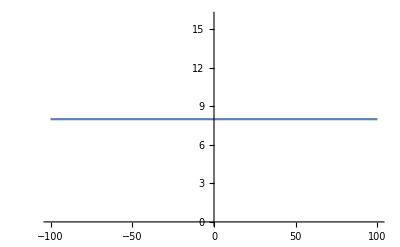

```mathematica
Plot[3x+4y-z=8, {x,-100,100}]
```

```mathematica
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

-Graphics-

Set::write: Tag Plus in -59.9975+8 y-z is Protected.

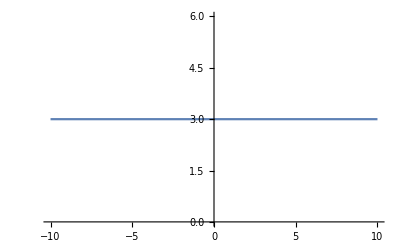

```mathematica
function2 =Plot[6x+8y-z=3, {x,-10,10}]
```

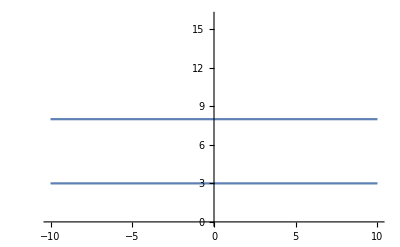

```mathematica
Show[function1,function2]
```

```mathematica
fun1  =Plot3D[3 x+4 y-z-8==0,{x,7,9},{y,7,9},PlotTheme->"Detailed",AxesLabel->{x,y,z},PlotStyle->Red]
```

-Graphics3D-

```mathematica
fun2 =Plot3D[6 x+8y-2z=3,{x,-10,10},{y,-10,10},PlotTheme->"Detailed",AxesLabel->{x,y,z},PlotStyle->Blue]
```

Set::write: Tag Plus in -79.9886-59.9914-2 z is Protected.

-Graphics3D-

```mathematica
Show[fun1,fun2]
```

-Graphics3D-

```mathematica
cd=ContourPlot3D[6x+8y-2z==3, {x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
gt=ContourPlot3D[3x+4y-z==8, {x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
Show[cd,gt]
```

-Graphics3D-

## 6. Uppgift 9

### Find the Eigenvalues for the following matrix. (9 | -4 | -2 | -2 -56 | 32 | -28 | 44 -14 | -14 | 6 | -14 42 | -33 | 21 | -45)

```mathematica
matrixA={{9,-4,-2,-4},{-56,32,-28,44 },{-14,-14,6,-14},{42,-33,21,-45}};
```

```mathematica
matrixA//MatrixForm
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

```mathematica
Eigenvalues[matrixA]
```

{13,13,-12,-12}

## 7. Uppgift 7

### Calculate A-B+C,ABC, and CBA . A=(3 7 2 | 2 12 5 | 4 0 2),B=(5 6 10 | 8 4 1 | 7 9 0),C=(5 5 6 | 22 9 8 | 5 7 2).

```mathematica
A={{3,2,4},{7,12,0},{2,5,2}};
```

```mathematica
B={{5,8,7},{6,4,9},{10,1,0}};
```

```mathematica
c={{5,22,5},{5,9,7},{6,8,2}};
```

```mathematica
result1=A-B+c
```

{{3,16,2},{6,17,-2},{-2,12,4}}

```mathematica
result1//MatrixForm
```

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

```mathematica
result2= A.B.c
```

{{749,2110,665},{1997,4546,1577},{844,2134,684}}

```mathematica
result2//MatrixForm
```

(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)

```mathematica
result3=c.B.A
```

{{2018,3175,1294},{1260,1874,828},{1096,1750,620}}

```mathematica
result3//MatrixForm
```

(2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)

## 8. Uppgift 18

### State the DiagonalMatrix D and matrices P and P^-1 of A. A=(-6 | 4 | 0 | 9 -3 | 0 | 1 | 6 -1 | -2 | 1 | 0 -4 | 4 | 0 | 7)

The following formula “A = PDP^-1” is used to solve the above mentioned problem.

```mathematica
A={{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}};
```

```mathematica
A//MatrixForm
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
Eigenvalues[A]
```

{5,-2,-2,1}

```mathematica
d={{5,0,0,0},{0,-2,0,0},{0,0,-2,0},{0,0,0,1}};
```

```mathematica
d=({{5, 0, 0, 0}, {0, -2, 0, 0}, {0, 0, -2, 0}, {0, 0, 0, 1}})
```

```mathematica
P =Transpose[Eigenvectors[A]];
P//MatrixForm
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

```mathematica
PInvers=Inverse[P];
```

```mathematica
PInvers//MatrixForm
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

```mathematica
Eigensystem[A]
```

```mathematica
{{5,-2,-2,1},

{{2,1,-1,2},
{6,-3,0,4},
{1,1,1,0},
{2,-1,-7,2}}}
```

```mathematica
P.d.PInvers//MatrixForm
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

## 9. Uppgift 1

```mathematica
place holder
```

## 10. Uppgift 1

```mathematica
dsf
```

```mathematica
a=({{6, 7, 8}, {9, 0, +}, {□, □, □}, {□, □, □}, {□, □, □}})
```